```mathematica
Remove["Global`*"]
```

```mathematica
$Assumptions=And@@Thread[{m1,m2,m3,s1,s2,s3,M,ρ, φ, Σ}>0];
```

```mathematica
V = {{1/s1^2, 0, 0},
{0, 1/s2^2, 0},
{0, 0, 1/s3^2}};
T = {{m1/(m1+m2 + m3), m2/(m1+m2 + m3), m3/(m1+m2 + m3)},
{1, -1, 0},
{-m1/(m1+m2), -m2/(m1+m2), 1}};
Tinv = Simplify[Inverse[T]];
norm = (1/(2Pi s1^2))^(3/2)(1/(2Pi s2^2))^(3/2)(1/(2Pi s3^2))^(3/2)
MatrixForm[V]
MatrixForm[T]
MatrixForm[Tinv]
Simplify[Det[T]]
```

((1/s1^2)^(3/2) (1/s2^2)^(3/2) (1/s3^2)^(3/2))/(16 √2 π^(9/2))

(1/s1^2 | 0 | 0
0 | 1/s2^2 | 0
0 | 0 | 1/s3^2)

(m1/(m1+m2+m3) | m2/(m1+m2+m3) | m3/(m1+m2+m3)
1 | -1 | 0
-m1/(m1+m2) | -m2/(m1+m2) | 1)

(1 | m2/(m1+m2) | -m3/(m1+m2+m3)
1 | -m1/(m1+m2) | -m3/(m1+m2+m3)
1 | 0 | (m1+m2)/(m1+m2+m3))

-1

```mathematica
P = Simplify[Transpose[Tinv].V.Tinv];
MatrixForm[P]
Simplify[Det[P]]
```

(1/s1^2+1/s2^2+1/s3^2 | (m2/s1^2-m1/s2^2)/(m1+m2) | (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2)/(m1+m2+m3)
(m2/s1^2-m1/s2^2)/(m1+m2) | (m2^2/s1^2+m1^2/s2^2)/(m1+m2)^2 | (m3 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)
(-m3/s1^2-m3/s2^2+(m1+m2)/s3^2)/(m1+m2+m3) | (m3 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2) | (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2)/(m1+m2+m3)^2)

1/(s1^2 s2^2 s3^2)

```mathematica
J = {R, r12, r312};
exp = -1/2 Simplify[Transpose[J].P.J];
(* the -2 in 'alpha' is necessary to match the definition of alpha in the formula for the gaussian integral *)
alpha = -2 * Coefficient[exp, R, 2] 
beta = Coefficient[exp, R, 1]
gamma = Coefficient[exp, R, 0]
```

1/s1^2+1/s2^2+1/s3^2

1/2 (-(2 r12 (m2/s1^2-m1/s2^2))/(m1+m2)-(2 r312 (-m3/s1^2-m3/s2^2+(m1+m2)/s3^2))/(m1+m2+m3))

1/2 (-(r12^2 (m2^2/s1^2+m1^2/s2^2))/(m1+m2)^2-(2 m3 r12 r312 (m1 s1^2-m2 s2^2))/((m1+m2) (m1+m2+m3) s1^2 s2^2)-(r312^2 (m3^2 (1/s1^2+1/s2^2)+(m1+m2)^2/s3^2))/(m1+m2+m3)^2)

Integrate over R via 3D gaussian integral. Using

```mathematica
GaussianIntegral3D[alpha_,beta_,gamma_]:=(2 Pi/alpha)^(3/2) Exp[gamma+beta^2/(2 alpha)]
```

```mathematica
SourcePdfJC = Simplify[ norm * GaussianIntegral3D[alpha, beta, gamma]]/. A_. Exp[arg_]:>A Exp[Collect[arg,r12,Simplify]];
(*SourcePdfJC = SourcePdfJC/. HoldPattern[s2^2 s3^2+s1^2 (s2^2+s3^2)]:>Σ^2 //Simplify*)
```

### Check normalization

```mathematica
a12 =  SourcePdfJC/. A_. Exp[arg_]:>-2*Coefficient[arg,r12,2] ;
b12 =  SourcePdfJC/. A_. Exp[arg_]:>Coefficient[arg,r12,1] ;
c12 =  SourcePdfJC/. A_. Exp[arg_]:>Coefficient[arg,r12,0] ;
N12 =  SourcePdfJC/. A_. Exp[arg_]:>A;
```

```mathematica
SourcePdfHC12 = N12 * GaussianIntegral3D[a12, b12, c12];
```

```mathematica
a312 =  SourcePdfHC12/. A_. Exp[arg_]:>-2*Coefficient[arg,r312,2] ;
b312 =  SourcePdfHC12/. A_. Exp[arg_]:>Coefficient[arg,r312,1] ;
c312 =  SourcePdfHC12/. A_. Exp[arg_]:>Coefficient[arg,r312,0] ;
N312 =  SourcePdfHC12/. A_. Exp[arg_]:>A;
```

```mathematica
N312 * GaussianIntegral3D[a312, b312, c312] //FullSimplify
```

1

## Move to hyperspherical coordinates

Build the argument of the exponent

```mathematica
mu12 = m1 m2 /(m1 + m2);
mu312 = m3(m1 + m2)/(m1 +m2+m3);
(*r12 = Sqrt[M/mu12]ρ Cos[φ];
r312 = Sqrt[M/mu312]ρ Sin[φ];*)
Clear[r12]
v1 = {r1 Sin[theta1] Cos[phi1] , r1 Sin[theta1]Sin[phi1] , r1 Cos[theta1]};
v2 = {r2 Sin[theta2] Cos[phi2] , r2 Sin[theta2]Sin[phi2] , r2 Cos[theta2]};
v1.v2 // FullSimplify
```

r1 r2 (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2])

```mathematica
arg = SourcePdfJC /. A_.Exp[arg_.] :> arg ;
(* Substitute Jacobi coordinates with hyperspherical coordinates *)
argHC = Coefficient[arg, r12, 2] * M/mu12 ρ^2 Cos[φ]^2+ 
Coefficient[arg, r312, 2] * M/mu312 ρ^2  Sin[φ]^2+ Coefficient[arg, (r12 * r312)]* M/Sqrt[mu12 * mu312]ρ^ 2 Cos[φ]Sin[φ]*(Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2])

(*argHC  =argHC/.r12-> Sqrt[M/mu12]ρ Cos[φ]
argHC = argHC /. r312 -> Sqrt[M/]ρ Sin[φ]*)
```

-(M (2 m1 m2 s3^2+m1^2 (s1^2+s3^2)+m2^2 (s2^2+s3^2)) ρ^2 Cos[φ]^2)/(2 m1 m2 (m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))+(M (-m1 s1^2+m2 s2^2) ρ^2 Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/((m1+m2) √((m1 m2 m3)/(m1+m2+m3)) (s2^2 s3^2+s1^2 (s2^2+s3^2)))+(M (m1+m2+m3) (-s1^2/(2 (s2^2 s3^2+s1^2 (s2^2+s3^2)))-s2^2/(2 (s2^2 s3^2+s1^2 (s2^2+s3^2)))) ρ^2 Sin[φ]^2)/((m1+m2) m3)

```mathematica
(M ρ^2 (-((m1^2 s1^2+m2^2 s2^2+(m1+m2)^2 s3^2) Cos[φ]^2)/(2 m1 m2)+1/(√((m1 m2 m3)/(m1+m2+m3)))(-m1 s1^2+m2 s2^2) Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ]-((m1+m2+m3) (s1^2+s2^2) Sin[φ]^2)/(2 m3)))/((m1+m2) (s2^2 s3^2+s1^2 (s2^2+s3^2)))-argHC // Simplify
```

0

```mathematica
jac = M^3/(mu12 mu312)^(3/2)ρ^5 * Sin[φ]^2 * Cos[φ]^2
```

```mathematica
(M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/((m1 m2 m3)/(m1+m2+m3))^(3/2)
```

```mathematica
$Assumptions = $Assumptions && Σ>0;
```

```mathematica
norm * Exp[argHC]/. (m1+m2+m3)->m3(m1 + m2)/m312 /. (m1 + m2) -> m1 m2 /m12 /. (s2^2 s3^2+s1^2 (s2^2+s3^2))->Σ^2 //Simplify
```

1/(8 π^3 Σ^3)ⅇ^(-1/(2 Σ^2)M ρ^2 ((m12 (2 m1 m2 s3^2+m1^2 (s1^2+s3^2)+m2^2 (s2^2+s3^2)) Cos[φ]^2)/(m1^2 m2^2)+(2 m12 (m1 s1^2-m2 s2^2) Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/(m1 m2 √(m12 m312))+((s1^2+s2^2) Sin[φ]^2)/m312))

```mathematica
norm= SourcePdfJC /. A_.Exp[arg_.] :> A;
SourcePdfHC =  jac  * norm * Exp[argHC];
(*SourcePdfHC = SourcePdfHC/. HoldPattern[s2^2 s3^2+s1^2 (s2^2+s3^2)]:>Σ^2 //Simplify;*)
```

The general 3B source is  where

```mathematica
$Assumptions = $Assumptions && Σ>0;
SourcePdfHC /. (m1+m2+m3)->m3(m1 + m2)/m312 /. (m1 + m2) -> m1 m2 /m12 /. (s2^2 s3^2+s1^2 (s2^2+s3^2))->Σ^2 //Simplify
```

1/(8 π^3 (m12 m312 Σ^2)^(3/2))ⅇ^(-1/(2 Σ^2)M ρ^2 ((m12 (2 m1 m2 s3^2+m1^2 (s1^2+s3^2)+m2^2 (s2^2+s3^2)) Cos[φ]^2)/(m1^2 m2^2)+(2 m12 (m1 s1^2-m2 s2^2) Cos[φ] (Cos[theta1] Cos[theta2]+Cos[phi1-phi2] Sin[theta1] Sin[theta2]) Sin[φ])/(m1 m2 √(m12 m312))+((s1^2+s2^2) Sin[φ]^2)/m312)) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2

### AAA Source

```mathematica
$Assumptions =$Assumptions && m>0&& s>0;
SourcePdfHCAAA = Integrate[SourcePdfHC /.m1->m /.m2->m /.m3->m /.s1->s /.s2->s /. s3->s //Simplify, {φ, 0, Pi/2}] * (4Pi)^2
```

(ⅇ^(-(M ρ^2)/(2 m s^2)) M^3 ρ^5)/(8 m^3 s^6)

```mathematica
$Assumptions = $Assumptions && M >0 && m>0&& s>0;
Integrate[SourcePdfHCAAA, {ρ, 0, Infinity}]
```

1

### AAB Source

```mathematica
$Assumptions = $Assumptions && m>0&& s>0;
integrand = SourcePdfHC/.m1->m /. m2->m /.s1->s/.s2->s  //Simplify
SourcePdfHCAAB =integrand * (4Pi)^2
```

(ⅇ^(-(M ρ^2 (m s^2+m3 (s^2+s3^2)+(-m s^2+m3 s3^2) Cos[2 φ]))/(2 m m3 s^2 (s^2+2 s3^2))) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/(8 π^3 ((m^2 m3 s^2 (s^2+2 s3^2))/(2 m+m3))^(3/2))

(2 ⅇ^(-(M ρ^2 (m s^2+m3 (s^2+s3^2)+(-m s^2+m3 s3^2) Cos[2 φ]))/(2 m m3 s^2 (s^2+2 s3^2))) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/(π ((m^2 m3 s^2 (s^2+2 s3^2))/(2 m+m3))^(3/2))

```mathematica
SourcePdfHCAABAvg = Integrate[SourcePdfHCAAB, {φ, 0, Pi/2}]
```

1/(8 m^3 s^3)ⅇ^(-(M ((m+m3) s^2+m3 s3^2) ρ^2)/(2 m m3 s^2 (s^2+2 s3^2))) M^3 ((2 m+m3)/(m3 s^2+2 m3 s3^2))^(3/2) ρ^5 Hypergeometric0F1Regularized[2,((m M s^2 ρ^2-M m3 s3^2 ρ^2)^2)/(4 (2 m m3 s^4+4 m m3 s^2 s3^2)^2)]

```mathematica
$Assumptions = $Assumptions && m>0 && s>0;
Integrate[SourcePdfHCAABAvg, {ρ, 0, Infinity}]
```

1

### AAA Source with resonances

```mathematica
SourcePdfHCAAAppp =(4Pi)^2*Integrate[ SourcePdfHC /.m1->m /. m2->m /.m3->m/.s1->sp/.s2->sp /.s3->sp //Simplify, {φ, 0, Pi/2},Assumptions->$Assumptions&&sp>0]
```

(ⅇ^(-(M ρ^2)/(2 m sp^2)) M^3 ρ^5)/(8 m^3 sp^6)

```mathematica
Integrate[SourcePdfHCAAAppp, {ρ, 0, Infinity},Assumptions->$Assumptions&&sp>0]
```

1

```mathematica
$Assumptions = $Assumptions && m>0 && sp>0 && sr>0;
SourcePdfHCAAAppr =(4Pi)^2 SourcePdfHC /.m1->m /. m2->m /.m3->m/.s1->sp/.s2->sp /.s3->sr //Simplify
```

(6 √3 ⅇ^(-(M ρ^2 (Cos[φ]^2/sp^2+(3 Sin[φ]^2)/(sp^2+2 sr^2)))/(2 m)) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/(m^3 π sp^3 (sp^2+2 sr^2)^(3/2))

```mathematica
SourcePdfHCAAAppr / (4Pi)^2/. M->m/2
```

(3 √3 ⅇ^(-1/4 ρ^2 (Cos[φ]^2/sp^2+(3 Sin[φ]^2)/(sp^2+2 sr^2))) ρ^5 Cos[φ]^2 Sin[φ]^2)/(64 π^3 sp^3 (sp^2+2 sr^2)^(3/2))

```mathematica
SourcePdfHCAAAppr / (4Pi)^2
```

(3 √3 ⅇ^(-(M ρ^2 (Cos[φ]^2/sp^2+(3 Sin[φ]^2)/(sp^2+2 sr^2)))/(2 m)) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/(8 m^3 π^3 sp^3 (sp^2+2 sr^2)^(3/2))

```mathematica
SourcePdfHCAAAprr/.sr->sp/.M->m/2
```

SourcePdfHCAAAprr

```mathematica
SourcePdfHCAAApprAvg = Integrate[SourcePdfHCAAAppr /.M->m/2, {φ, 0, Pi/2} ,Assumptions->$Assumptions&&sp>0&&sr>0 && sp>sr]
```

(3 √3 ⅇ^(-((2 sp^2+sr^2) ρ^2)/(4 sp^2 (sp^2+2 sr^2))) ρ^5 Hypergeometric0F1Regularized[2,((sp^2-sr^2)^2 ρ^4)/(64 sp^4 (sp^2+2 sr^2)^2)])/(64 sp^3 (sp^2+2 sr^2)^(3/2))

```mathematica
SourcePdfHCAAApprAvg = Integrate[SourcePdfHCAAAppr, {φ, 0, Pi/2} ,Assumptions->$Assumptions&&sp>0&&sr>0 && sp>sr]/.M->m/2
```

(3 √3 ⅇ^(-((2 sp^2+sr^2) ρ^2)/(4 sp^2 (sp^2+2 sr^2))) ρ^3 BesselI[1,((sp-sr) (sp+sr) ρ^2)/(4 sp^2 (sp^2+2 sr^2))])/(8 sp (sp-sr) (sp+sr) √(sp^2+2 sr^2))

```mathematica
(3 √3 ⅇ^(-((2 sp^2+sr^2) ρ^2)/(4 sp^2 (sp^2+2 sr^2))) ρ^3 BesselI[1,((sp-sr) (sp+sr) ρ^2)/(4 sp^2 (sp^2+2 sr^2))])/(8 sp (sp-sr) (sp+sr) √(sp^2+2 sr^2))
```

(3 √3 ⅇ^(-((2 sp^2+sr^2) ρ^2)/(4 sp^2 (sp^2+2 sr^2))) ρ^3 BesselI[1,((sp-sr) (sp+sr) ρ^2)/(4 sp^2 (sp^2+2 sr^2))])/(8 sp (sp-sr) (sp+sr) √(sp^2+2 sr^2))

```mathematica
Integrate[SourcePdfHCAAAppr, {ρ, 0, Infinity} ,Assumptions->$Assumptions&&sp>0&&sr>0 && sp>sr]
```

(12 √3 sp^3 (sp^2+2 sr^2)^(3/2) Sin[2 φ]^2)/(π ((sp^2+2 sr^2) Cos[φ]^2+3 sp^2 Sin[φ]^2)^3)

```mathematica
Integrate[SourcePdfHCAAAppr, {φ, 0, Pi/2}, {ρ, 0, Infinity} ,Assumptions->$Assumptions&&sp>0&&sr>0  && sr>sp]
```

1

```mathematica
Plot3D[SourcePdfHCAAAppr /.sp->1 /.sr->2/.M->m/2, {ρ, 0, 10}, {φ, 0, Pi/2}]
```

-Graphics3D-

```mathematica
$Assumptions = $Assumptions && m>0 && sp>0 && sr>0;
SourcePdfHCAAAprr =(4Pi)^2 SourcePdfHC /.m1->m /. m2->m /.m3->m/.s1->sr/.s2->sr /.s3->sp //Simplify
```

(6 √3 ⅇ^(-(M ρ^2 (sp^2+2 sr^2+(sp^2-sr^2) Cos[2 φ]))/(2 m sr^2 (2 sp^2+sr^2))) M^3 ρ^5 Cos[φ]^2 Sin[φ]^2)/(m^3 π sr^3 (2 sp^2+sr^2)^(3/2))

```mathematica
Integrate[SourcePdfHCAAAprr, {φ, 0, Pi/2}, {ρ, 0, Infinity}, Assumptions->$Assumptions&&sp>0&&sr>0]
```

ConditionalExpression[1, sp≠sr]

```mathematica
SourcePdfHCAAAprrAvg = Integrate[SourcePdfHCAAAprr, {φ, 0, Pi/2}, Assumptions->$Assumptions&&sp>0&&sr>0 && sp>sr]/.M->m/2
```

(3 √3 ⅇ^(-((sp^2+2 sr^2) ρ^2)/(4 sr^2 (2 sp^2+sr^2))) ρ^5 Hypergeometric0F1Regularized[2,((sp^2-sr^2)^2 ρ^4)/(64 sr^4 (2 sp^2+sr^2)^2)])/(64 sr^3 (2 sp^2+sr^2)^(3/2))

```mathematica
Plot3D[SourcePdfHCAAAprr /.sp->1 /.sr->2/.M->m/2, {ρ, 0, 10}, {φ, 0, Pi/2}]
```

-Graphics3D-

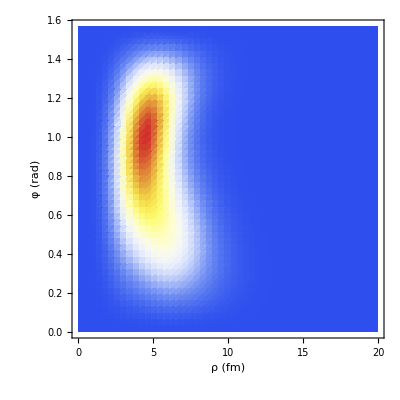

```mathematica
DensityPlot[SourcePdfHCAAAprr+SourcePdfHCAAAppr /.sp->1 /.sr->2/.M->m/2,{ρ,0,20},{φ,0,Pi/2},ColorFunction->"TemperatureMap", PlotRange->Full, PlotPoints->50, FrameLabel->{"ρ (fm)", "φ (rad)"}]
```

```mathematica
SourcePdfHCAAAppp
```

(ⅇ^(-(M ρ^2)/(2 m sp^2)) M^3 ρ^5)/(8 m^3 sp^6)

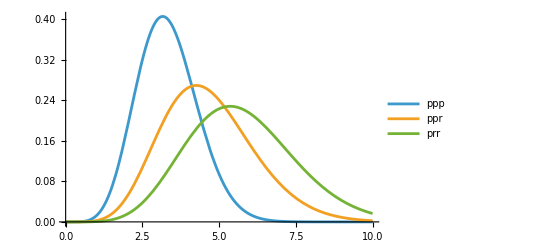

```mathematica
Plot[{SourcePdfHCAAAppp/. M->m/2/.sp->1, SourcePdfHCAAApprAvg/.sp->1/.sr->2, SourcePdfHCAAAprrAvg/.sp->1/.sr->2} , {ρ, 0, 10}, PlotLegends->{ppp, ppr, prr}]
```

```mathematica
test = Limit[SourcePdfHCAAApprAvg, sr->sp]/.sp->1
```

Limit::alimv: Warning: Assumptions that involve the limit variable are ignored.

1/64 ⅇ^(-ρ^2/4) ρ^5

```mathematica
SourcePdfHCAAAppp/. M->m/2/.sp->1
```

1/64 ⅇ^(-ρ^2/4) ρ^5

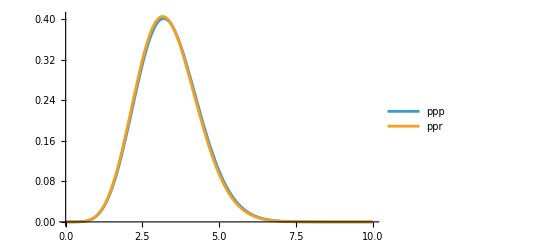

```mathematica
Plot[{SourcePdfHCAAAppp/. M->m/2/.sp->1.01, test} , {ρ, 0, 10}, PlotLegends->{ppp, ppr}]
```